```mathematica
SetDirectory["/home/kamano/gitsrc/ChemicalStructureRecognition"]
```

/home/kamano/gitsrc/ChemicalStructureRecognition

## Images

```mathematica
cdata=ChemicalData[];
```

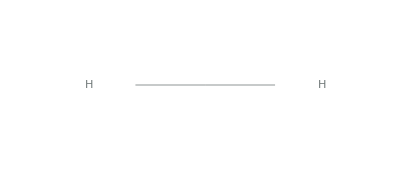

```mathematica
ChemicalData[cdata[[1]]]
```

```mathematica
r[1]=Rasterize[ChemicalData[cdata[[1]]],RasterSize->300,ImageSize->100]
```

-Graphics-

```mathematica
Information[r[1]]
```

Image

```mathematica
br[1]=Binarize[r[1]]
```

-Graphics-

```mathematica
Export["OSRA-test/br1.jpg",br[1]]
```

OSRA-test/br1.jpg

```mathematica
s=ChemicalData[cdata[[1]],"SMILES"]
```

[HH]

### train test

```mathematica
NetTrain[{1->s,1->s}]
```

NetTrain[{1→[HH],1→[HH]}]